```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
b[t_]=Sqrt[1+t^2];
τ[t_]=ArcTan[t];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
t ≥0;
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ψ, A][x_,y_,t_,κ_]=E^(I*π*(1-κ)*HeavisideTheta[y-x])*Subscript[ψ, F][x,y,t];
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
ρ[x_,y_,κ_]=Subscript[ρ, F][x,y]-Sign[y-x]*(E^(-Sign[y-x]*I*π*κ)+1)*Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],x,y}];
Subscript[ρ, A][x_,y_,t_,κ_]=1/b[t]*ρ[x/b[t],y/b[t],κ]*E^(-I*(b'[t](x^2-y^2))/(2*b[t]));
Subscript[n, A][p_,t_,κ_] := 2/(2π)*NIntegrate[E^(I*p*(x-y))Subscript[ρ, A][x,y,t,κ],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->9,PrecisionGoal->9];
```

```mathematica
Subscript[dataSet, 1]={5.603346248826138*^-7,6.559514570816137*^-7,7.728858528334441*^-7,7.728857656272661*^-7,6.559515510904031*^-7,5.603344045935865*^-7};
Subscript[dataSet, 2]={4.005831221691524*^-7,4.6890482827339017*^-7,5.52445303159744*^-7,5.524491188545782*^-7,4.689053797475611*^-7,4.00583583446506*^-7};
Subscript[dataSet, 3]={1.9766561989964088*^-7,2.313523542395843*^-7,2.7253739800494076*^-7,2.7253826590564994*^-7,2.3135228780588644*^-7,1.976653281748585*^-7};
Subscript[dataSet, 4]={1.382919073949338*^-7,1.759344889938252*^-7,1.7272550074988064*^-7,1.4421405606617888*^-7};
Subscript[dataSet, 5]={1.1264061555460077*^-7,6.324269988356478*^-8,6.157323050853562*^-8,5.056108624087825*^-8};
Subscript[dataSet, 6]={6.254411628501336*^-8,3.2203361793864246*^-8,6.105583484974382*^-8,-1.8696896640404918*^-10};
Subscript[dataSet, 7]={1.4691771704450663*^-6,1.806114122226376*^-6,1.8060900000954912*^-6,1.4686849620674337*^-6};
Subscript[dataSet, 8]={8.206390047679052*^-7,1.010006666506956*^-6,1.0070729413937105*^-6,8.171570144209059*^-7};
Subscript[dataSet, 9]={2.7328978507924284*^-7,3.354306737442996*^-7,3.358153269938354*^-7,2.7311931751534116*^-7};
```

```mathematica
(* Evaluate n(p,t) at various points to extract momentum tail coefficient *)
(*Pdomain =  Union[Range[-26,-24,1],Range[24,26,1]];*)
Pdomain=Union[Range[-20,-19,1],Range[19,20,1]];
Tdomain={0,.5,1,2,3,4,.25,.75,1.5};
Subscript[dataSet, m_]:=Subscript[n, A][Pdomain, Tdomain[[m]],1/2];
Do[Subscript[dataSet, i]=Re[Subscript[dataSet, i]];Print[Subscript[dataSet, i]],{i,1,Length[Tdomain]}];
```

{5.60335×10^-7,6.55951×10^-7,7.72886×10^-7,7.72886×10^-7,6.55952×10^-7,5.60334×10^-7}

{4.00583×10^-7,4.68905×10^-7,5.52445×10^-7,5.52449×10^-7,4.68905×10^-7,4.00584×10^-7}

{1.97666×10^-7,2.31352×10^-7,2.72537×10^-7,2.72538×10^-7,2.31352×10^-7,1.97665×10^-7}

{1.38292×10^-7,1.75934×10^-7,1.72726×10^-7,1.44214×10^-7}

{1.12641×10^-7,6.32427×10^-8,6.15732×10^-8,5.05611×10^-8}

{6.25441×10^-8,3.22034×10^-8,6.10558×10^-8,-1.86969×10^-10}

{1.46918×10^-6,1.80611×10^-6,1.80609×10^-6,1.46868×10^-6}

{8.20639×10^-7,1.01001×10^-6,1.00707×10^-6,8.17157×10^-7}

{2.7329×10^-7,3.35431×10^-7,3.35815×10^-7,2.73119×10^-7}

```mathematica
Pdomain1 =  Union[Range[-26,-24,1],Range[24,26,1]];
Pdomain2=Union[Range[-20,-19,1],Range[19,20,1]];
Do[Subscript[dataSet, i]=Subscript[dataSet, i]*Pdomain1^4*1/((2/π)^(3/2)*Cos[π/4]^2),{i,1,3}]
Do[Subscript[dataSet, i]=Subscript[dataSet, i]*Pdomain2^4*1/((2/π)^(3/2)*Cos[π/4]^2),{i,4,Length[Tdomain]}]
CoeffDep={};
Do[CoeffDep=Append[CoeffDep,Mean[Subscript[dataSet, i]]],{i,1,Length[Tdomain]}]
TailCoeff=Interpolation[Thread[{Tdomain,CoeffDep}]];
```

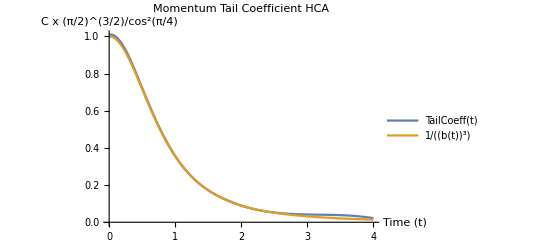

Export::nodir: Directory C:\Users\Tim\Documents\PhysicsResearch\UltraColdAtoms\ does not exist.

Export::noopen: Cannot open C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/HCA-MomentumTailCoeffTimeDep.png.

$Failed

```mathematica
p1=Plot[{TailCoeff[t],b[t]^(-3)},{t,0,4},PlotLabel->"Momentum Tail Coefficient HCA",AxesLabel->{"Time (t)", "C x (π/2)^(3/2)/cos^2(π/4)"},PlotLegends->"Expressions",ImageSize->Scaled[.5]]
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/HCA-MomentumTailCoeffTimeDep.png",p1]
```

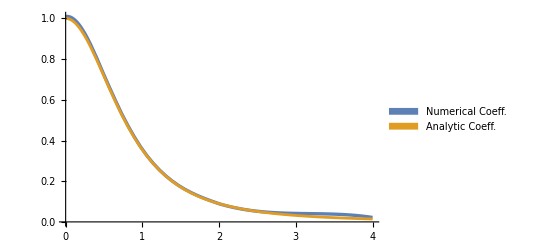

E:/Z/UltraColdAtoms/Plots/HCA-MomentumTailCoeffTimeDepPoster.png

```mathematica
p1=Plot[{TailCoeff[t],b[t]^(-3)},{t,0,4},PlotLegends->SwatchLegend[{"Numerical Coeff.","Analytic Coeff."},LabelStyle->{FontWeight->Bold,FontFamily-> "Helvetica",FontSize-> 26}],PlotStyle->{Thickness[.006],Thickness[.005]},ImageSize->Scaled[0.6],BaseStyle->{FontWeight->Bold,FontFamily-> "Helvetica",FontSize-> 26}, AxesStyle->Thick]
Export["E:/Z/UltraColdAtoms/Plots/HCA-MomentumTailCoeffTimeDepPoster.png",p1]
```